```mathematica
$Assumptions = x1 ∈Reals&& x2∈Reals&&x3∈Reals&&x4 ∈Reals&& s∈Reals
ϕ[x1_,x2_,x3_,x4_,s_] ={ x1^2 + (x2 - s)^2, (x3-x1)^2+(x4-x2)^2}
```

x1∈ℝ&&x2∈ℝ&&x3∈ℝ&&x4∈ℝ&&s∈ℝ

{x1^2+(-s+x2)^2,(-x1+x3)^2+(-x2+x4)^2}

```mathematica
Dϕ = D[ϕ[x1,x2,x3,x4,s],{{x1,x2,x3,x4}}];
Dϕinverse=%//PseudoInverse //FullSimplify ;
%//MatrixForm
```

((x1^3-2 x1^2 x3+x1 (x3^2+(s+x2-2 x4) (x2-x4))-(s-x2) x3 (x2-x4))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2)))) | ((s-x2) (s (x1-x3)+x2 x3-x1 x4))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2))))
(-s (2 (x1-x3)^2+(x2-x4)^2)+x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2)))) | (x1 (s (x1-x3)+x2 x3-x1 x4))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2))))
((x1-x3) (x1^2-x1 x3-(s-x2) (x2-x4)))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2)))) | -((x1^2+(s-x2)^2) (x1-x3))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2))))
((x1^2-x1 x3-(s-x2) (x2-x4)) (x2-x4))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2)))) | -((x1^2+(s-x2)^2) (x2-x4))/(2 (x1^4-2 x1^3 x3+s^2 (2 (x1-x3)^2+(x2-x4)^2)+x2^2 (2 x3^2+(x2-x4)^2)-2 x1 x2 x3 (x2+x4)-2 s (x2 (2 x3^2+(x2-x4)^2)+x1^2 (x2+x4)-x1 x3 (3 x2+x4))+x1^2 (x3^2+2 (x2^2-x2 x4+x4^2)))))

```mathematica
ϕ' = (D[ϕ[x1,x2,x3,x4,s[t]],t])/.{s'[t] -> s', s[t]->s};
%//MatrixForm
ϕ'' = (D[ϕ[x1,x2,x3,x4,s[t]],{t,2}])/.{s'[t] -> s', s[t]->s};
```

(-2 (-s+x2) s'
0)

```mathematica
Simplify[- Dϕinverse.ϕ',x1^2 + (x2 - s)^2==1&&(x3-x1)^2+(x4-x2)^2&&s'==1]
```

{-(((s-x2) (x1^3-2 x1^2 x3-(s-x2) x3 (x2-x4)+x1 (x2^2+x3^2+s (x2-x4)-3 x2 x4+2 x4^2)))/(-x1^4+x2^2+2 x1^3 x3+2 x3^2-2 x2 x4+x4^2+x1^2 (2-x2^2-x3^2+2 s (x2-x4)+x4^2)+2 x1 x3 (-2+x2^2-x2 x4+s (-x2+x4)))),((s-x2) (-x1^2 (x2+x4)+x1 x3 (3 x2+x4)-x2 (x2^2+2 x3^2-2 x2 x4+x4^2)+s (2 x1^2+x2^2-4 x1 x3+2 x3^2-2 x2 x4+x4^2)))/(-x1^4+x2^2+2 x1^3 x3+2 x3^2-2 x2 x4+x4^2+x1^2 (2-x2^2-x3^2+2 s (x2-x4)+x4^2)+2 x1 x3 (-2+x2^2-x2 x4+s (-x2+x4))),-(((x1-x3) (s x1 (x1-x3)+x2 (-1+x1 x3)+x4-x1^2 x4))/(-x1^4+x2^2+2 x1^3 x3+2 x3^2-2 x2 x4+x4^2+x1^2 (2-x2^2-x3^2+2 s (x2-x4)+x4^2)+2 x1 x3 (-2+x2^2-x2 x4+s (-x2+x4)))),-(((x2-x4) (s x1 (x1-x3)+x2 (-1+x1 x3)+x4-x1^2 x4))/(-x1^4+x2^2+2 x1^3 x3+2 x3^2-2 x2 x4+x4^2+x1^2 (2-x2^2-x3^2+2 s (x2-x4)+x4^2)+2 x1 x3 (-2+x2^2-x2 x4+s (-x2+x4))))}

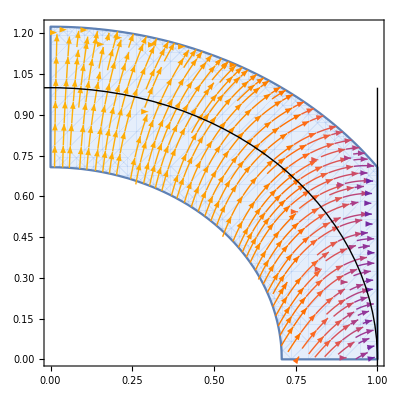

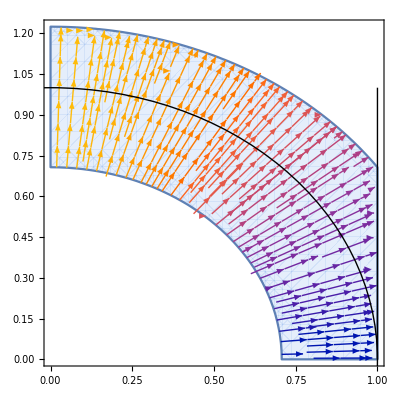

```mathematica
rhs = - Dϕinverse.ϕ'/.{s'->1, s->(-Sqrt[1-x1^2]+x2)};
rhs1 ={rhs[[1]],rhs[[2]]}/.{x3->0,x4->0};
rhs2 ={rhs[[3]],rhs[[4]]}/.{x1->0,x2->0};
StreamPlot[rhs1,{x1,x2}∈ImplicitRegion[.5 <= x1^2 + x2^2 <= 1.5&& 1>=x1>=0 && x2 >=0,{x1,x2}],Background->White,StreamPoints->Fine];
Show[%,
Graphics[Circle[]],
Graphics[Line[
{{1,0},{1,1}}
]
]
]
StreamPlot[rhs2,{x3,x4}∈ImplicitRegion[.5 <= x3^2 + x4^2 <= 1.5&& 1>=x3>=0 && x4 >=0,{x3,x4}],Background->White,StreamPoints->Fine];
Show[%,
Graphics[Circle[]],
Graphics[Line[
{{1,0},{1,1}}
]
]
]
```